## 3D - Quadratic (ellipse) cross section

{0.5,0.1}

29.8555

29.8555

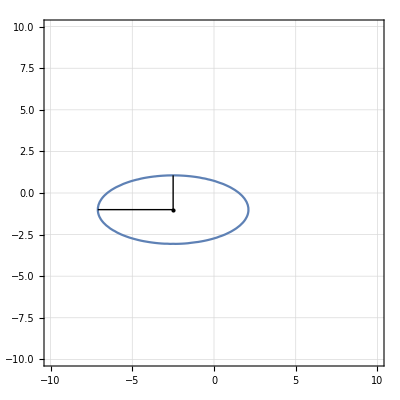

```mathematica
Clear["Global`*"]

a = 0.1;
b = 0;
c = 0.5;
d =0.5;
ee =1;
f = -1;
p0x = 0;
p0y = 0;
(*Ellipse[a_,b_,c_,d_,ee_,f_, p0x_, p0y_] *)

EM = {{a,b/2},{b/2,c}};
ev = {d, ee};
p = {x ,y};
p0 = {p0x, p0y};
eq1 =Expand[(p-p0)ᵀ .EM . (p-p0) + ev.(p-p0)+f  ];

eigs = Eigenvalues[EM]
v = Eigenvectors[EM];

aell =-Sqrt[2*(a*ee^2 + c*d^2 - b*d*ee +(b^2 - 4*a*c)*f)*((a + c) + Sqrt[(a-c)^2 + b^2])]/(b^2 - 4*a*c);
bell =-Sqrt[2*(a*ee^2 + c*d^2 - b*d*ee +(b^2 - 4*a*c)*f)*((a + c) - Sqrt[(a-c)^2 + b^2])]/(b^2 - 4*a*c);
pc ={ (2*c*d - b*ee)/(b^2 - 4*a*c), (2*a*ee - b*d)/(b^2 - 4*a*c)} + p0;

cont = ContourPlot[eq1==0,{x,-10,10},{y,-10,10}, GridLines->Automatic];
pt = Graphics[Point[pc]];

arr1= Graphics[ Line[{pc,pc + bell*Normalize[v[[1]]]}]];
arr2= Graphics[ Line[{pc,pc + aell*Normalize[v[[2]]]}]];
 Pi*aell*bell
Pi*(4*a*c + c*d^2 +a *ee^2)/(4*c*a*Sqrt[c*a])
Show[cont,pt, arr1, arr2]
```

```mathematica
Clear["Global`*"]
(*b=0;*)
f=-1;
(*d=0;
ee=0;*)

EE = {{a,b/2},{b/2,c}};
Eigenvalues[EE];
Det[EE]

aell =-Sqrt[2*(a*ee^2 + c*d^2 - b*d*ee +(b^2 - 4*a*c)*f)*((a + c) + Sqrt[(a-c)^2 + b^2])]/(b^2 - 4*a*c)
bell =-Sqrt[2*(a*ee^2 + c*d^2 - b*d*ee +(b^2 - 4*a*c)*f)*((a + c) - Sqrt[(a-c)^2 + b^2])]/(b^2 - 4*a*c);
pc ={ (2*c*d - b*ee)/(b^2 - 4*a*c), (2*a*ee - b*d)/(b^2 - 4*a*c)} + p0

FullSimplify[aell*bell];
```

-b^2/4+a c

-(√2 √((a+√(b^2+(a-c)^2)+c) (-b^2+4 a c+c d^2-b d ee+a ee^2)))/(b^2-4 a c)

{(2 c d-b ee)/(b^2-4 a c)+p0,(-b d+2 a ee)/(b^2-4 a c)+p0}

## 2D - Linear cross section

1

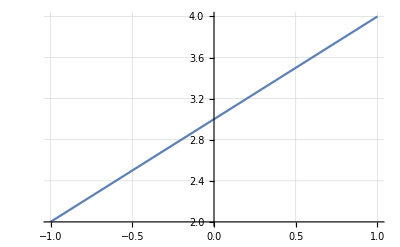

```mathematica
Clear["Global`*"]
a = 1;
d =3;
f = 1
eq1 =Expand[x*a + d ];
cont = Plot[eq1,{x,-1,1}, GridLines->Automatic];
Show[cont]
```

## Semialgebraic sets

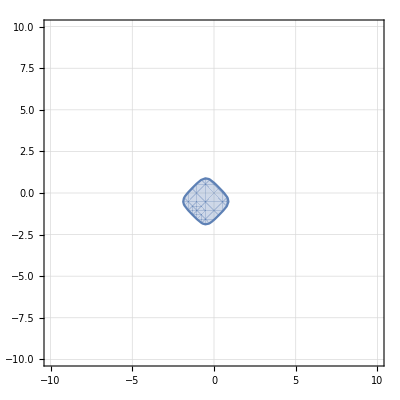

```mathematica
Clear["Global`*"]

a = 1;
b = 1;
c = 1;
d =1;
ee =1;
f = 1;
g = 1;
h = 1;
ii = 1;
ct = 1;
(*S = DiagonalMatrix[{a,b,c,d,ee,f, g, h ,ii}];*)
(*Eigenvalues[S];*)
lim = 10;

eq1 = ct *(a* x^2*y^2 +b*x^2 +c* y^2 + ee*x^2*y  + f*x*y^2   + g*x*y + h*x + ii*y) -1;
GraphicsRow[{Plot3D[{eq1,y},{x,-lim,lim},{y,-lim,lim},BoxRatios->1,FaceGrids->All],RegionPlot[eq1<=0,{x,-lim,lim},{y,-lim,lim}, GridLines->Automatic]}]
```

## Polynomial basis

4

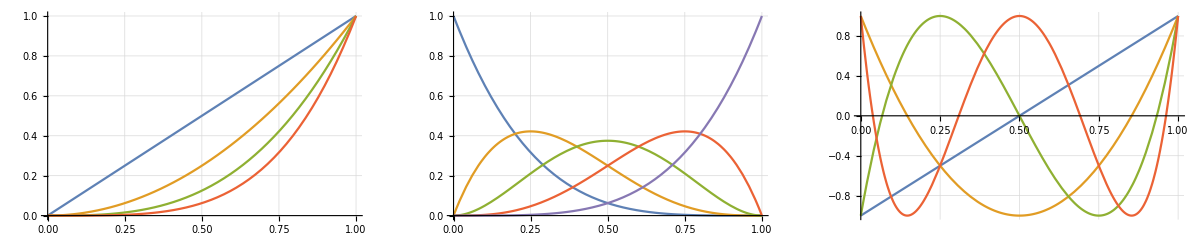

```mathematica
Clear["Global`*"]
deg=4
plotNominal =Plot[Evaluate[Table[x^i,{i,1,deg}]],{x,0,1}, GridLines->Automatic];
plotBernstein = Plot[Evaluate[Table[Binomial[deg,k]*x^k*(1-x)^(deg-k),{k,0,deg}]],{x,0,1}, GridLines->Automatic];
plotChebyshev =Plot[Evaluate[Table[Cos[i*ArcCos[2*x -1]],{i,1,deg}]],{x,0,1}, GridLines->Automatic];
GraphicsRow[{plotNominal,plotBernstein, plotChebyshev}]
```